```mathematica
SetDirectory[NotebookDirectory[]];
```

## p10q3

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
```

```mathematica
datadir="../Processed_Data/9_FiniteSizeAnalysis_AFM";
```

```mathematica
(*a0v0d8small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0_amag1_U0.8_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d8small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.4_amag1_U0.8_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d8small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.6_amag1_U0.8_AFMGenerationTrend.txt"],"Data"]]])[[1]];*)
```

```mathematica
(*a0v0d85small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0_amag1_U0.85_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d85small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.4_amag1_U0.85_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d85small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.6_amag1_U0.85_AFMGenerationTrend.txt"],"Data"]]])[[1]];*)
```

```mathematica
(*a0v0d75small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0_amag1_U0.75_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d75small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.4_amag1_U0.75_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d75small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.6_amag1_U0.75_AFMGenerationTrend.txt"],"Data"]]])[[1]];*)
```

```mathematica
a0v0d7small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0_amag1_U0.7_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d7small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.4_amag1_U0.7_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d7small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.6_amag1_U0.7_AFMGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d65small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0_amag1_U0.65_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d65small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.4_amag1_U0.65_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d65small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.6_amag1_U0.65_AFMGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
(*a0v0d8large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0_amag1_U0.8_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d8large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.4_amag1_U0.8_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d8large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.6_amag1_U0.8_AFMGenerationTrend.txt"],"Data"]]])[[1]];*)
```

```mathematica
(*a0v0d85large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0_amag1_U0.85_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d85large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.4_amag1_U0.85_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d85large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.6_amag1_U0.85_AFMGenerationTrend.txt"],"Data"]]])[[1]];*)
```

```mathematica
(*a0v0d75large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0_amag1_U0.75_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d75large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.4_amag1_U0.75_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d75large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.6_amag1_U0.75_AFMGenerationTrend.txt"],"Data"]]])[[1]];*)
```

```mathematica
a0v0d7large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0_amag1_U0.7_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d7large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.4_amag1_U0.7_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d7large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.6_amag1_U0.7_AFMGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d65large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0_amag1_U0.65_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d65large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.4_amag1_U0.65_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d65large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.6_amag1_U0.65_AFMGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
nsmall={0,1,2};
nlarge={0,1,2,3};
```

```mathematica
psize=0.03;
lthickness=0.006;
```

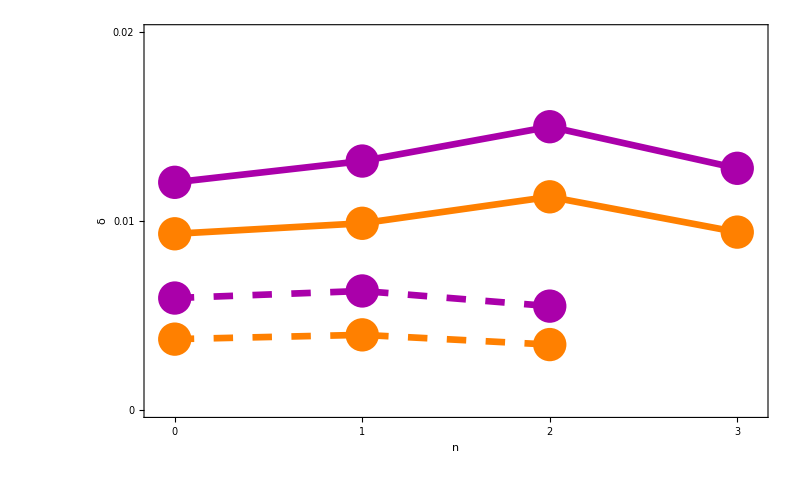

```mathematica
xrange={-0.1,3.1};
yrange={0,0.02};
Show[
ListPlot[Transpose@{nsmall,a0v0d65small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0v0d65small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0v0d65large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0v0d65large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0v0d7small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0v0d7small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0v0d7large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0v0d7large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.01,0.02},None},{{0,1,2,3},None}},FrameTicksStyle->FontSize->50
]
```

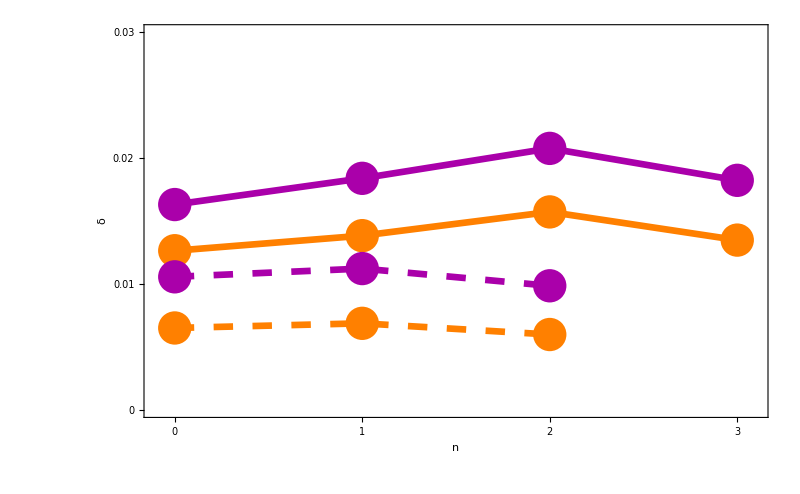

```mathematica
xrange={-0.1,3.1};
yrange={0,0.03};
Show[
ListPlot[Transpose@{nsmall,a0d4v0d65small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d4v0d65small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d4v0d65large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d4v0d65large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0d4v0d7small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d4v0d7small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d4v0d7large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d4v0d7large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.01,0.02,0.03},None},{{0,1,2,3},None}},FrameTicksStyle->FontSize->50
]
```

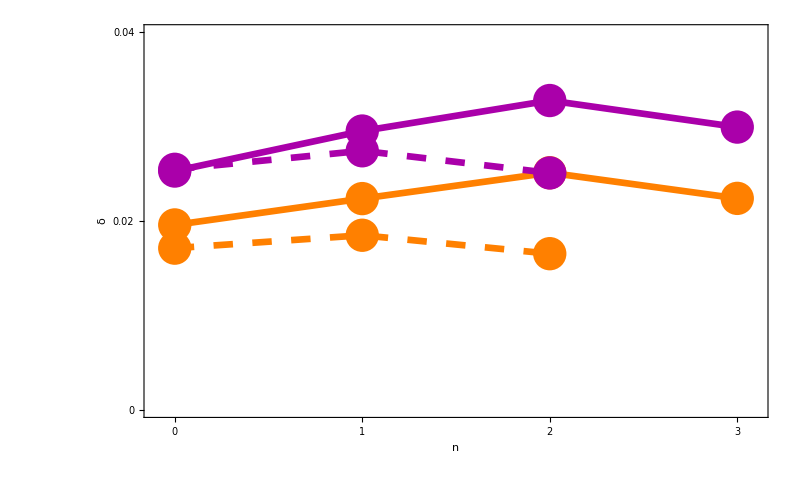

```mathematica
xrange={-0.1,3.1};
yrange={0,0.04};
Show[
ListPlot[Transpose@{nsmall,a0d6v0d65small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d6v0d65small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d6v0d65large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d6v0d65large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0d6v0d7small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d6v0d7small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d6v0d7large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d6v0d7large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.02,0.04},None},{{0,1,2,3},None}},FrameTicksStyle->FontSize->50
]
```

## p14q3

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
```

```mathematica
datadir="../Processed_Data/9_FiniteSizeAnalysis_AFM";
```

```mathematica
a0v0d7small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0_amag1.2_U0.7_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d7small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0.4_amag1.2_U0.7_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d7small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0.6_amag1.2_U0.7_AFMGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d65small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0_amag1.2_U0.65_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d65small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0.4_amag1.2_U0.65_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d65small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0.6_amag1.2_U0.65_AFMGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d7large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0_amag1.2_U0.7_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d7large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0.4_amag1.2_U0.7_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d7large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0.6_amag1.2_U0.7_AFMGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d65large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0_amag1.2_U0.65_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d65large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0.4_amag1.2_U0.65_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d65large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0.6_amag1.2_U0.65_AFMGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
nsmall={0,1};
nlarge={0,1,2};
```

```mathematica
psize=0.03;
lthickness=0.006;
```

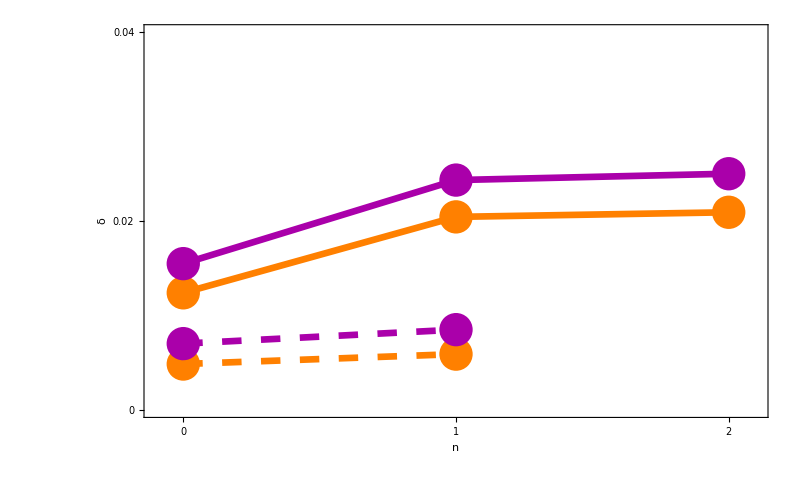

```mathematica
xrange={-0.1,2.1};
yrange={0,0.04};
Show[
ListPlot[Transpose@{nsmall,a0v0d65small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0v0d65small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0v0d65large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0v0d65large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0v0d7small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0v0d7small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0v0d7large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0v0d7large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.02,0.04},None},{{0,1,2,3},None}},FrameTicksStyle->FontSize->50
]
```

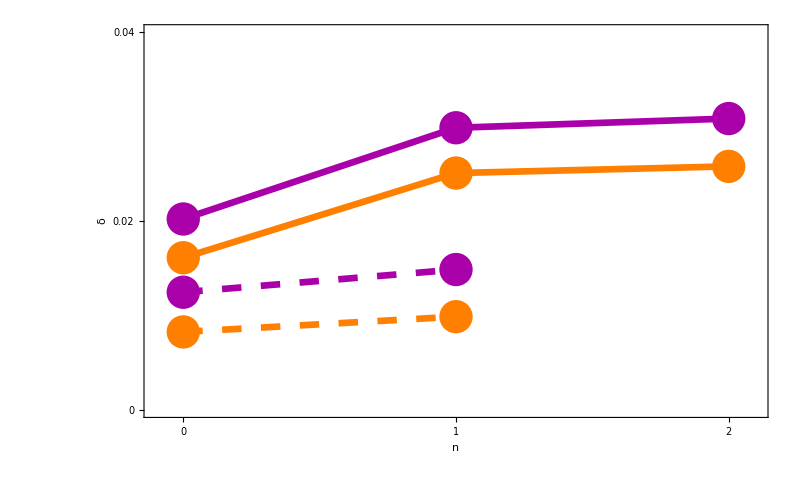

```mathematica
xrange={-0.1,2.1};
yrange={0,0.04};
Show[
ListPlot[Transpose@{nsmall,a0d4v0d65small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d4v0d65small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d4v0d65large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d4v0d65large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0d4v0d7small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d4v0d7small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d4v0d7large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d4v0d7large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.02,0.04},None},{{0,1,2,3},None}},FrameTicksStyle->FontSize->50
]
```

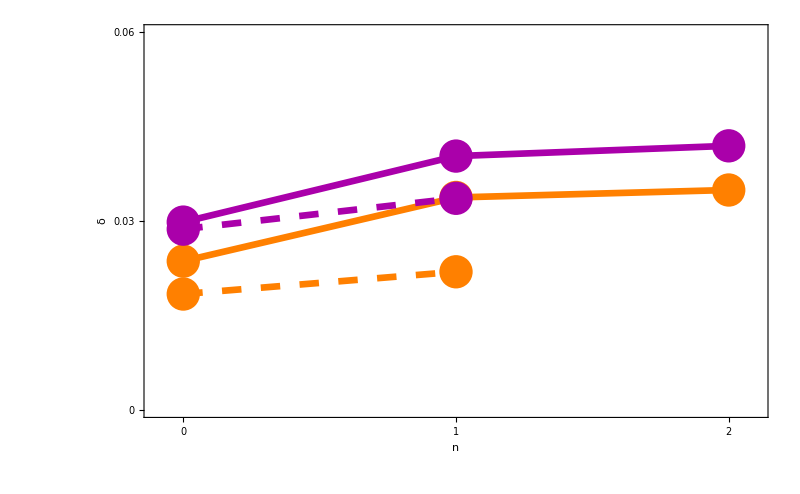

```mathematica
xrange={-0.1,2.1};
yrange={0,0.06};
Show[
ListPlot[Transpose@{nsmall,a0d6v0d65small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d6v0d65small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d6v0d65large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d6v0d65large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0d6v0d7small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d6v0d7small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d6v0d7large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d6v0d7large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.03,0.06},None},{{0,1,2,3},None}},FrameTicksStyle->FontSize->50
]
```

## Honeycomb

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
```

```mathematica
datadir="../Processed_Data/9_FiniteSizeAnalysis_AFM";
```

```mathematica
a0v1small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl19a0_amag0.5_U1_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v1small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl19a0.4_amag0.5_U1_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v1small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl19a0.6_amag0.5_U1_AFMGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v1d1small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl19a0_amag0.5_U1.1_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v1d1small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl19a0.4_amag0.5_U1.1_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v1d1small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl19a0.6_amag0.5_U1.1_AFMGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v1large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl20a0_amag0.5_U1_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v1large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl20a0.4_amag0.5_U1_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v1large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl20a0.6_amag0.5_U1_AFMGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v1d1large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl20a0_amag0.5_U1.1_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v1d1large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl20a0.4_amag0.5_U1.1_AFMGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v1d1large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl20a0.6_amag0.5_U1.1_AFMGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
nsmall=Range[0,18,1];
nlarge=Range[0,19,1];
```

```mathematica
psize=0.03;
lthickness=0.006;
```

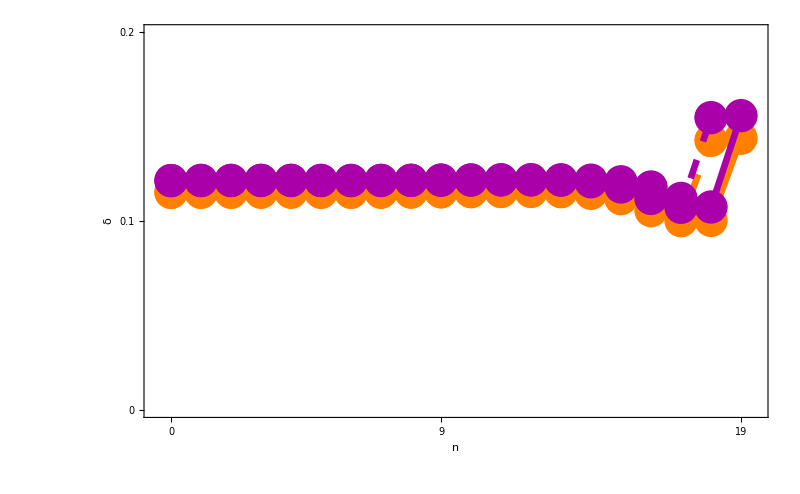

```mathematica
xrange={-0.5,19.5};
yrange={0,0.2};
Show[
ListPlot[Transpose@{nsmall,a0v1small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0v1small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0v1large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0v1large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0v1d1small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0v1d1small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0v1d1large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0v1d1large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.1,0.2},None},{{0,9,19},None}},FrameTicksStyle->FontSize->50
]
```

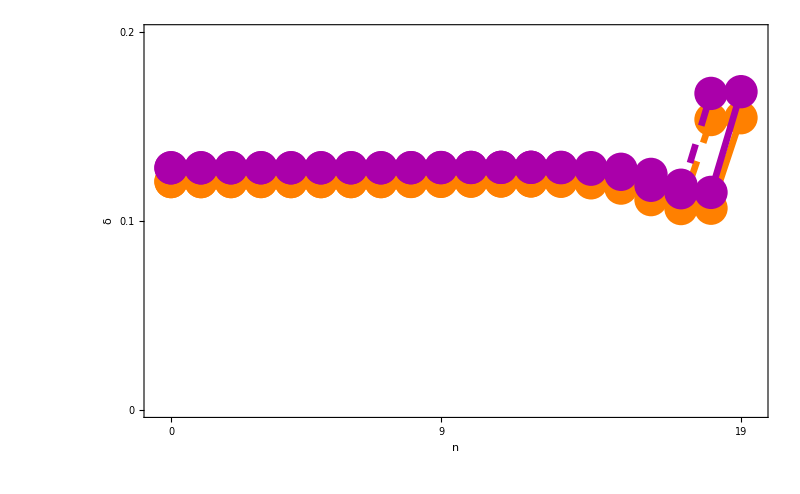

```mathematica
xrange={-0.5,19.5};
yrange={0,0.2};
Show[
ListPlot[Transpose@{nsmall,a0d4v1small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d4v1small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d4v1large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d4v1large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0d4v1d1small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d4v1d1small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d4v1d1large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d4v1d1large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.1,0.2},None},{{0,9,19},None}},FrameTicksStyle->FontSize->50
]
```

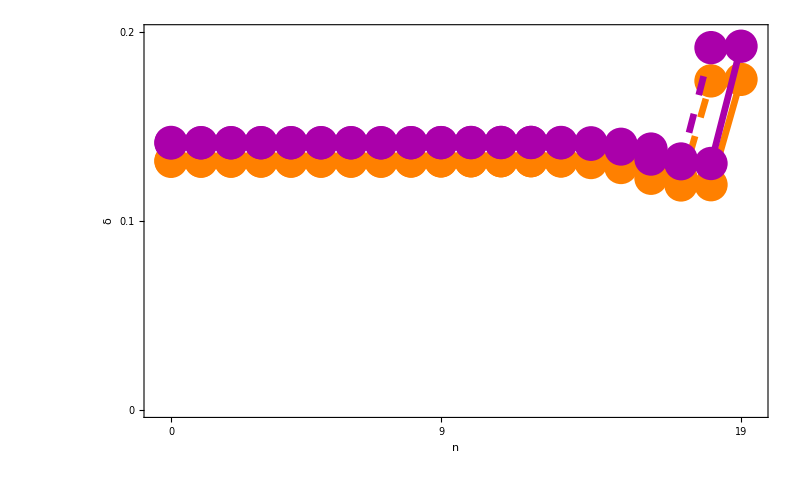

```mathematica
xrange={-0.5,19.5};
yrange={0,0.2};
Show[
ListPlot[Transpose@{nsmall,a0d6v1small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d6v1small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d6v1large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d6v1large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0d6v1d1small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d6v1d1small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d6v1d1large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d6v1d1large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.1,0.2},None},{{0,9,19},None}},FrameTicksStyle->FontSize->50
]
```